# Ecological Viability Decomposition

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll["Global`*"]
Quiet[<<"Path/to/Dynamica.m"]
(* The Dynamica package for standard dynamical systems analyses was created by Randall Beer and can be found at his personal website: https://rdbeer.pages.iu.edu/ *)
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

## System Definition

```mathematica
M2 = DynamicalSystem[{
-A*(1 - A/b)(1 - A/k1)-((f A)/(h^2+A^2))*A*S,
e((f A)/(h^2+A^2))*A*S - e*S 
},
{{A,-0.00001,5},{S,-0.00001,1}},
{{e,0.001,1},{h,0.001,3},{f,1,2},{k1,0.01,10},{b,0.01,3}}];
M2 = M2/.{f->1.5,b->1, e->0.8,h->1, k1->1.6};
```

```mathematica
M2via = DynamicalSystem[{
-A*(1 - A/b)(1 - A/k1)-((f A)/(h^2+A^2))*A*S,
e((f A)/(h^2+A^2))*A*S - e*S 
},
{{A,0.5,5},{S,0.05,1}},
{{e,0.001,1},{h,0.001,3},{f,1,2},{k1,0.01,10},{b,0.01,3}}];
M2via = M2via/.{f->1.5,b->1, e->0.8,h->1, k1->1.6};
```

```mathematica
M2a = DynamicalSystem[{
-A*(1 - A/b)(1 - A/k1)
},
{{A,-0.00001,5}},
{{k1,0.01,10},{b,0.01,3}}];
```

```mathematica
M2a = M2a/.{k1->1.6,b->1};
```

```mathematica
revM2 = DynamicalSystem[{
-(-A*(1 - A/b)(1 - A/k1)-((f A)/(h^2+A^2))*A*S),
-(e((f A)/(h^2+A^2))*A*S - e*S ) 
},
{{A,-0.00001,4},{S,-0.00001,1}},
{{e,0.001,1},{h,0.001,3},{f,1,2},{k1,0.01,10},{b,0.01,3}}];
```

```mathematica
revM2 = revM2/.{f->1.5,b->1, e->0.8,h->1, k1->1.6};
```

```mathematica
dA2[A_,S_]:=-A*(1 - A/b)(1 - A/k1)-((f* A)/(h^2+A^2))*A*S;
dS2[A_,S_]:=e((f*A)/(h^2+A^2))*A*S - e*S ;
F2[{A_,S_}]:={dA2[A,S],dS2[A,S]}
```

## Analysis

### Time Series

```mathematica
f=1.5;b=1;e=0.8;h=1; k1=1.6;
```

```mathematica
TS=NDSolveValue[
{A'[t]== -A[t]*(1 - A[t]/b)(1 - A[t]/k1)-((f A[t])/(h^2+A[t]^2))*A[t]*S[t],
S'[t] == e((f A[t])/(h^2+A[t]^2))*A[t]*S[t] - e*S[t]  ,
A[0]==4,S[0]==0.14},{A,S},{t,0,1000}];
```

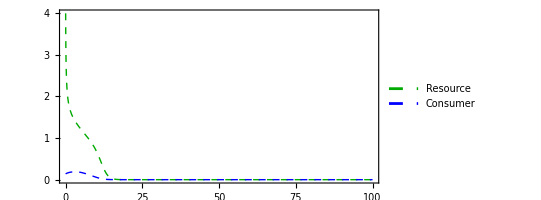

```mathematica
Plot[Evaluate[#[t]& /@TS],{t,0,100},PlotRange->All,
 PlotStyle->{{Darker[Green],Thick, Dashed},{Blue,Thick, Dashed}},
PlotLegends->{"Resource","Consumer"},TicksStyle->10,AspectRatio->1/2, LabelStyle->16, Frame->True,  FrameStyle->Black]
```

### Viability Definitions

```mathematica
Clear[f,b, e,h, k1];
alow = 0.5;
slow = 0.05;
```

```mathematica
v1[A_]:=A-alow
v2[S_]:=S-slow
```

```mathematica
boundary=Show[ListLinePlot[{{alow,0},{alow,100}},PlotStyle->{Thickness[0.01],/@{"#00BFFF"}}],
ListLinePlot[{{0,slow},{100,slow}},PlotStyle->{Thickness[0.01],/@{"#00BFFF"}}]];
```

### Dynamical Analysis

```mathematica
xx = DisplayPhasePortrait[M2,SaddleManifolds->True,SaddleManifoldDuration->10000,SaddleManifoldStyle->Thick];
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 49.5225 and t = 49.5242.

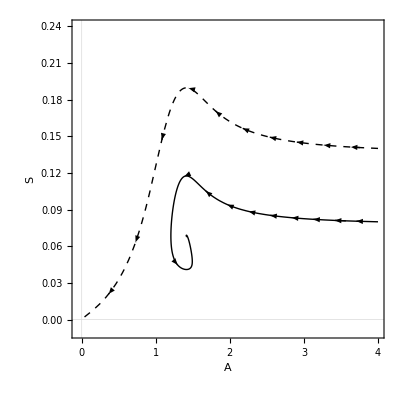

```mathematica
Show[
DisplayTrajectories[M2,{{4,0.08}},100,PlotStyle->{Black},Arrows->10],
DisplayTrajectories[M2,{{4,0.14}},100,PlotStyle->{Black,Dashed},Arrows->10],
LabelStyle->{Black,16},PlotRange->{{-0.05,4},{-0.01,0.24}},
GridLines->{{0},{0}}, GridLinesStyle->Thin
]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 49.5225 and t = 49.5242.

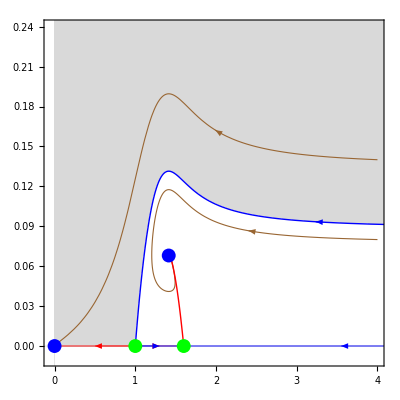

{EquilibriumPoint[Stable,Node,{0,0}],EquilibriumPoint[Saddle,Node,{1.,0}],EquilibriumPoint[Stable,Spiral,{1.41421,0.0680195}],EquilibriumPoint[Saddle,Node,{1.6,0}]}

```mathematica
Show[
RegionPlot[x>-0.1,{x,0,5},{y,0,0.6}, PlotStyle->LightGray,BoundaryStyle->None],
ListPlot[xx[[1]][[2]][[1]][[1]][[3]][[1]],PlotStyle->None,Joined->True,Filling->Bottom,FillingStyle->White],
DisplayTrajectories[M2,{{4,0.14},
{4,0.08}},100],
DisplayPhasePortrait[M2,SaddleManifolds->True,SaddleManifoldDuration->10000,SaddleManifoldStyle->Thick],
(*boundary,*)
LabelStyle->{Black,16},PlotRange->{{-0.05,4},{-0.01,0.24}},
GridLines->{{0},{0}}, GridLinesStyle->Thin
]
$PhasePortraitEPs
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 49.5225 and t = 49.5242.

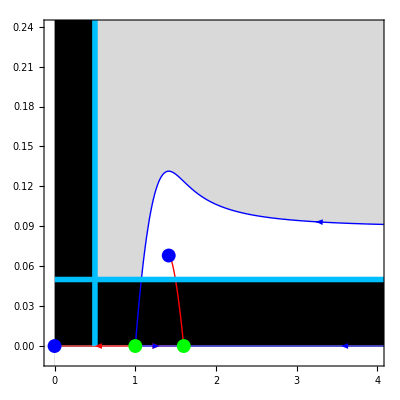

{EquilibriumPoint[Stable,Node,{0,0}],EquilibriumPoint[Saddle,Node,{1.,0}],EquilibriumPoint[Stable,Spiral,{1.41421,0.0680195}],EquilibriumPoint[Saddle,Node,{1.6,0}]}

```mathematica
Show[
RegionPlot[x>-0.1,{x,0,5},{y,0,0.6}, PlotStyle->LightGray,BoundaryStyle->None],
ListPlot[xx[[1]][[2]][[1]][[1]][[3]][[1]],PlotStyle->None,Joined->True,Filling->Bottom,FillingStyle->White],
RegionPlot[x<0.5,{x,0,0.5},{y,0,0.25}, PlotStyle->Black,BoundaryStyle->None],
RegionPlot[y<0.24,{x,0,4.2},{y,0,0.05}, PlotStyle->Black,BoundaryStyle->None],
DisplayPhasePortrait[M2,SaddleManifolds->True,SaddleManifoldDuration->10000,SaddleManifoldStyle->Thick],
boundary,
LabelStyle->{Black,16},PlotRange->{{-0.05,4},{-0.01,0.24}},
GridLines->{{0},{0}}, GridLinesStyle->Thin
]
$PhasePortraitEPs
```

### Adding Minimum Viable Populations

```mathematica
startA = alow;
maxA = 4;
granA = 0.01;
startS = slow; (* 0.24 *)
maxS = 0.24;
granS = 0.001;
outcomes = {};
```

```mathematica
For[i=(startA/granA),i<=(maxA/granA),i++,
For[j=(startS/granS),j<=(maxS/granS),j++,
bin = 0 (* 0: both survive, 1: only A survives, 2: S dies first, 3: A dies first *);
DisplayTrajectories[M2,{{i*granA,j*granS}},50, PlotPoints->2000];
trajA = $Trajectories[[1]][[All,1]];
minA = Min[trajA];
Adex = Position[trajA, SelectFirst[$Trajectories[[1]][[All,1]],#<alow&]][[1]][[1]];
trajS = $Trajectories[[1]][[All,2]];
minS = Min[trajS];
Sdex = Position[trajS, SelectFirst[$Trajectories[[1]][[All,2]],#<slow&]][[1]][[1]];
(*Print[{minA, minS, Adex, Sdex}];*)

If[minA>alow && minS > slow,
(* Both survive *)
bin = 0,
If[minA>alow,
(* only A survives *)
bin = 1,
If[Adex < Sdex ,
(* A dies first *)
bin = 3,
(* S dies first, sim A from where S dies to see if it survives*) 
DisplayTrajectories[M2a,{{trajA[[Sdex]]}},100];
traja = $Trajectories[[1]][[All,1]];
mina = Min[traja];
If[mina>alow,
bin=1,
bin=2];
];
];
];
(*Print[{minA,Adex,minS,Sdex,bin}];*)
AppendTo[outcomes,{i, j,bin}];
]
]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Export["vdat.dat",outcomes];
```

```mathematica
outcomes=Import["vdat.dat","Data"];
```

```mathematica
outcomes
```

```mathematica
VPlot =ListDensityPlot[Transpose[ArrayReshape[outcomes[[All,3]],{IntegerPart[(maxA/granA) - (startA/granA)+1],IntegerPart[(maxS/granS)-(startS/granS)+1]}]],DataRange->{{startA,maxA},{startS,maxS}},ColorFunction->(If[#<1,White,ColorData["GrayTones",1-#/8]]&),ColorFunctionScaling->False,
InterpolationOrder->0, PlotLegends->None]
```

-Graphics-

```mathematica
Show[
RegionPlot[x<0.5,{x,0,4},{y,0,0.24}, PlotStyle->Black,BoundaryStyle->None],
RegionPlot[y<0.24,{x,0,4},{y,0,0.24}, PlotStyle->Black,BoundaryStyle->None],
VPlot,
boundary,
DisplayPhasePortrait[M2,SaddleManifolds->True,SaddleManifoldDuration->10000, SaddleManifoldStyle->Thick],
LabelStyle->{Black,16},PlotRange->{{0,4},{0,0.24}},AspectRatio->1
]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 49.5225 and t = 49.5242.

-Graphics-

### Mortality, Ordering, & Collapse Manifolds

```mathematica
f=1.5;b=1; e=0.8;h=1; k1=1.6;
vectors = {{4,0.05},{3.8,0.05},{3.6,0.05},
{3.4,0.05},{3.2,0.05},{3,0.05},{2.8,0.05},{2.6,0.05},
{2.4,0.05},{2.2,0.05},{2,0.05},{1.8,0.05},{1.6,0.05},
{1.4,0.05},{1.2,0.05},{1,0.05},{0.8,0.05},{0.6,0.05},
{0.5,0.05},
{0.5,0.062},{0.5,0.074},{0.5,0.086},{0.5,0.098},{0.5,0.11},
{0.5,0.122},{0.5,0.134},{0.5,0.146},{0.5,0.158},{0.5,0.17},
{0.5,0.182},{0.5,0.194},{0.5,0.206},{0.5,0.218},{0.5,0.23}
};
```

```mathematica
Show[
RegionPlot[x<0.5,{x,0,4},{y,0,0.24}, PlotStyle->Black,BoundaryStyle->None],
RegionPlot[y<0.24,{x,0,4},{y,0,0.24}, PlotStyle->Black,BoundaryStyle->None],
VPlot,
boundary,
VectorPlot[{dA2[A,S],dS2[A,S]},{A,0,4},{S,0,0.24},VectorSizes->0.9,VectorColorFunction->None,VectorStyle->Yellow,VectorPoints->vectors],
AspectRatio->1,PlotRange->{{0,4},{0,0.24}},PlotRangeClipping->True,Frame->True,PlotLegends->None,LabelStyle->Directive[Black, 16]]
```

-Graphics-

```mathematica
startA = 1.3;
maxA = 1.5;
granA = 0.001;
startS = 0.05; (* 0.24 *)
maxS = 0.057;
granS = 0.00005;
outcomesA = {};
```

```mathematica
For[i=(startA/granA),i<=(maxA/granA),i++,
For[j=(startS/granS),j<=(maxS/granS),j++,
bin = 0 (* 0: both survive, 1: only A survives, 2: S dies first, 3: A dies first *);
DisplayTrajectories[M2,{{i*granA,j*granS}},50, PlotPoints->2000];
trajA = $Trajectories[[1]][[All,1]];
minA = Min[trajA];
Adex = Position[trajA, SelectFirst[$Trajectories[[1]][[All,1]],#<alow&]][[1]][[1]];
trajS = $Trajectories[[1]][[All,2]];
minS = Min[trajS];
Sdex = Position[trajS, SelectFirst[$Trajectories[[1]][[All,2]],#<slow&]][[1]][[1]];
(*Print[{minA, minS, Adex, Sdex}];*)

If[minA>alow && minS > slow,
(* Both survive *)
bin = 0,
If[minA>alow,
(* only A survives *)
bin = 1,
If[Adex < Sdex ,
(* A dies first *)
bin = 3,
(* S dies first, sim A from where S dies to see if it survives*) 
DisplayTrajectories[M2a,{{trajA[[Sdex]]}},100];
traja = $Trajectories[[1]][[All,1]];
mina = Min[traja];
If[mina>alow,
bin=1,
bin=2];
];
];
];
(*Print[{minA,Adex,minS,Sdex,bin}];*)
AppendTo[outcomesA,{i, j,bin}];
]
]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Export["vdatA.dat",outcomesA];
```

```mathematica
outcomesA=Import["vdatA.dat","Data"];
```

```mathematica
outcomesA
```

```mathematica
VPlotA =ListDensityPlot[Transpose[ArrayReshape[outcomesA[[All,3]],{IntegerPart[(maxA/granA) - (startA/granA)+1],IntegerPart[(maxS/granS)-(startS/granS)+1]}]],DataRange->{{startA,maxA},{startS,maxS}},ColorFunction->(If[#<1,White,ColorData["GrayTones",1-#/8]]&),ColorFunctionScaling->False,
InterpolationOrder->0, PlotLegends->None];
```

```mathematica
vectors1a = {{1.31,0.05},{1.33,0.05},
{1.35,0.05},{1.37,0.05},{1.385,0.05}};
vectors1b={{1.4142,0.05},{0,0}};
vectors1c={{1.435,0.05},
{1.45,0.05},{1.47,0.05},{1.49,0.05}};
```

```mathematica
Show[
RegionPlot[x<0.5,{x,0,4},{y,0,0.24}, PlotStyle->Black,BoundaryStyle->None],
RegionPlot[y<0.24,{x,0,4},{y,0,0.24}, PlotStyle->Black,BoundaryStyle->None],
VPlotA,
boundary,
VectorPlot[{dA2[A,S],dS2[A,S]},{A,0,4},{S,0,0.24},VectorSizes->0.07,VectorColorFunction->None,VectorStyle->{Purple,Arrowheads[0.04],Thick},VectorPoints->vectors1a],
VectorPlot[{dA2[A,S],dS2[A,S]},{A,0,4},{S,0,0.24},VectorSizes->0.07,VectorColorFunction->None,VectorStyle->{Green,Arrowheads[0.04],Thick},VectorPoints->vectors1c],
VectorPlot[{dA2[A,S],dS2[A,S]},{A,0,4},{S,0,0.24},VectorSizes->0.07,VectorColorFunction->None,VectorStyle->{Magenta,Arrowheads[0.06],Thick},VectorPoints->vectors1b],
AspectRatio->1/2,PlotRange->{{1.31,1.49},{0.048,0.056}},PlotRangeClipping->True,Frame->True,PlotLegends->None,LabelStyle->{Black,20}]
```

-Graphics-

```mathematica
startA = 0.5;
maxA = 0.55; 
granA = 0.0002;
startS = 0.05;
maxS = 0.055;
granS = 0.00005;
outcomesB = {};
```

```mathematica
For[i=(startA/granA),i<=(maxA/granA),i++,
For[j=(startS/granS),j<=(maxS/granS),j++,
bin = 0 (* 0: both survive, 1: only A survives, 2: S dies first, 3: A dies first *);
DisplayTrajectories[M2,{{i*granA,j*granS}},50, PlotPoints->10000];
trajA = $Trajectories[[1]][[All,1]];
minA = Min[trajA];
Adex = Position[trajA, SelectFirst[$Trajectories[[1]][[All,1]],#<alow&]][[1]][[1]];
trajS = $Trajectories[[1]][[All,2]];
minS = Min[trajS];
Sdex = Position[trajS, SelectFirst[$Trajectories[[1]][[All,2]],#<slow&]][[1]][[1]];
(*Print[{minA, minS, Adex, Sdex}];*)

If[minA>alow && minS > slow,
(* Both survive *)
bin = 0,
If[minA>alow,
(* only A survives *)
bin = 1,
If[Adex < Sdex ,
(* A dies first *)
bin = 3,
(* S dies first, sim A from where S dies to see if it survives*) 
DisplayTrajectories[M2a,{{trajA[[Sdex]]}},100,PlotPoints->100];
traja = $Trajectories[[1]][[All,1]];
mina = Min[traja];
If[mina>alow,
bin=1,
bin=2];
];
];
];
(*Print[{minA,Adex,minS,Sdex,bin}];*)
AppendTo[outcomesB,{i, j,bin}];
]
]
```

```mathematica
Export["vdatB.dat",outcomesB];
```

```mathematica
outcomesB=Import["vdatB.dat","Data"];
```

```mathematica
VPlotB =ListDensityPlot[Transpose[ArrayReshape[outcomesB[[All,3]],{IntegerPart[(maxA/granA) - (startA/granA)+1],IntegerPart[(maxS/granS)-(startS/granS)+1]}]],DataRange->{{startA,maxA},{startS,maxS}},ColorFunction->(If[#<1,White,ColorData["GrayTones",1-#/8]]&),ColorFunctionScaling->False,
InterpolationOrder->0, PlotLegends->None];
```

```mathematica
vectors2a = {
{0.5,0.051},{0.5,0.052},{0.5,0.053},{0.5,0.054},
{0.5,0.05},{0.505,0.05},{0.51,0.05},{0.515,0.05},
{0.52,0.05},{0.525,0.05},{0.53,0.05},{0.535,0.05},
{0.54,0.05},{0.545,0.05}
};
vectors2b = {
{0.5,0.05},{0,0}
};
```

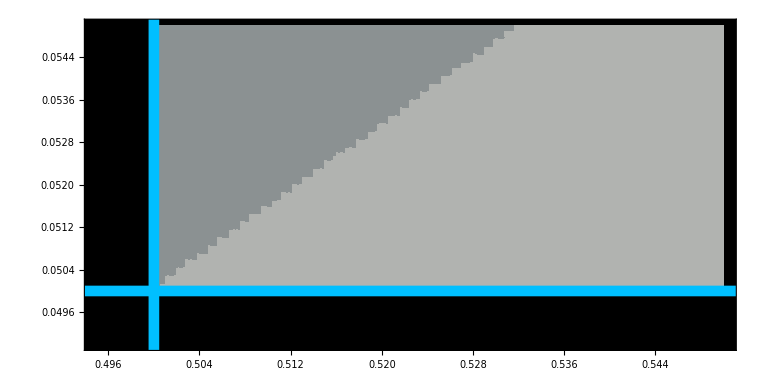

```mathematica
Show[
RegionPlot[x<0.5,{x,0,4},{y,0,0.24}, PlotStyle->Black,BoundaryStyle->None],
RegionPlot[y<0.24,{x,0,4},{y,0,0.24}, PlotStyle->Black,BoundaryStyle->None],
VPlotB,
boundary,
VectorPlot[{dA2[A,S],dS2[A,S]},{A,0,4},{S,0,0.24},VectorSizes->0.04,VectorColorFunction->None,VectorStyle->{Purple,Arrowheads[0.04]},VectorPoints->vectors2a],
VectorPlot[{dA2[A,S],dS2[A,S]},{A,0,4},{S,0,0.24},VectorSizes->0.04,VectorColorFunction->None,VectorStyle->{Cyan,Arrowheads[0.06],Thick},VectorPoints->vectors2b],
AspectRatio->1/2,PlotRange->{{0.495,0.55},{0.049,0.055}},PlotRangeClipping->True,Frame->True,PlotLegends->None,LabelStyle->{Black,24}]
```

```mathematica
Solve[Dot[F2[{A,S}]/.{f->1.5,b->1.6, e->0.8,h->1, k1->1},{-1,0}]==0 && v1[A]==0,{A,S},PositiveReals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{}

```mathematica
Solve[Dot[F2[{A,S}]/.{f->1.5,b->1.6, e->0.8,h->1, k1->1},{0,-1}]==0 && v2[S]==0,{A,S},PositiveReals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{A→1.41421,S→0.05}}

```mathematica
Show[
RegionPlot[x<0.5,{x,0,4},{y,0,0.24}, PlotStyle->Black,BoundaryStyle->None],
RegionPlot[y<0.24,{x,0,4},{y,0,0.24}, PlotStyle->Black,BoundaryStyle->None],
VPlot,
boundary,
(* Mortality Manifold *)
DisplayTrajectories[revM2,{{1.414213562373095,slow}},200,PlotPoints->50,MaxStepSize->0.001,MaxSteps->Infinity,PlotStyle->{Magenta,Thick},Arrows->False],
(* Ordering Manifold *)
DisplayTrajectories[revM2,{{alow,slow}},200,PlotPoints->30,PlotStyle->{Cyan, Thick},Arrows->False],
(* Collapse Manifold *)
(*DisplayTrajectories[revM2,{{1,slow}},200,PlotPoints->30,PlotStyle->{Red, Dashed, Thick},Arrows->False],*)
(* Standard Dynamical Analysis *)
DisplayPhasePortrait[M2via(*,SaddleManifolds->True,SaddleManifoldDuration->10000, SaddleManifoldStyle->Thick*)],
LabelStyle->{Black,16},PlotRange->{{0,4},{0,0.24}},AspectRatio->1
]
```

First::nofirst: {} has zero length and no first element.

-Graphics-

```mathematica
DisplayPhasePortrait[M2a, PlotRange-> {-0.1,4}, LabelStyle->{Black,16}]
```

DisplayPhasePortrait::optx: Unknown option {LabelStyle} in {PlotRange→{-0.1,4},LabelStyle→{color,16}}.

-Graphics-